Potential

```mathematica
V[r_] = 1/2w^2r^2
Veff[r_] = 1/(8r^2) + V[r]
r0 = 1/Sqrt[2w]
r[x_] = x+r0

Veffbar[x_] = Simplify[Veff[r[x]] - Veff[r0]]
```

(r^2 w^2)/2

1/(8 r^2)+(r^2 w^2)/2

1/(√2 √w)

1/(√2 √w)+x

(2 w^2 x^2 (2+2 √2 √w x+w x^2))/(√2+2 √w x)^2

First Coefficient

```mathematica
Eminustwo = Veff[r0]
```

w/2

Second Coefficient

```mathematica
phiminusone [x_] = Assuming[x>=0&&w>0,FullSimplify[-Sqrt[2Veffbar[x]]]]
Eminusone = -1/2 phiminusone'[0] -1/(2 r0^2)
```

-(2 w x √(2+2 √2 √w x+w x^2))/(√2+2 √w x)

0

```mathematica
phiminusone'[0]
```

-2 w

```mathematica
Limit[FullSimplify[1/2phiminusone'[x]+1/(2*r[x]*r[x])+Eminusone]/Assuming[x>=0&&w>0,FullSimplify[Sqrt[2Veffbar[x]]]],x->0]
```

-(√w)/(√2)

```mathematica
D[]
```

Third Coefficient

```mathematica
phizero[x_] = Assuming[x>0&& w>0,Simplify[(1/2phiminusone'[x]+1/(2*r[x]*r[x])+Eminusone)/-phiminusone[x]]]

Ezero = -1/2Limit[phizero'[x],x->0]-1/2Limit[phizero[x]^2,x->0]+3/(8r0^2)
```

```mathematica
D[√(2+2 √2 √w x+w x^2),x] /. x->0
```

√w

```mathematica
Limit[-(√2+3 √w x+2 √2 w x^2+w^(3/2) x^3-√(2+2 √2 √w x+w x^2))/(2 √2 x+8 √w x^2+5 √2 w x^3+2 w^(3/2) x^4),x->0]
```

-(√w)/(√2)

Energy

```mathematica
E = Simplify[Eminustwo k^2 + Eminusone k + Ezero ]
```

Set::wrsym: Symbol ⅇ is Protected.

-2 ebar^4 (3+2 k+k^2)

```mathematica
r[2]
```

2+1/(4 ebar^2)

```mathematica
2+1/(4 ebar^2)
```

2+1/(4 ebar^2)

```mathematica
coeff [x_] =-phiminusone[x]
Simplify[(1/2 phizero'[x] +1/2phizero[x]phizero[x]-3/(8)r[x]^(-2)+Ezero)]
phione[x_] = Simplify[(1/2 phizero'[x] +1/2phizero[x]^2-3/(8r[x]^2)+Ezero)/coeff[x]]
phione'[x]
Eone =Limit[ -1/2phione'[x]-1/2(phione[x]phizero[x]+phione[x]phizero[x]),x->0]
a = {Eminustwo,Eminusone,Ezero,Eone}
b = {phiminusone,phizero,phione}
```

(2 w x √(2+2 √2 √w x+w x^2))/(√2+2 √w x)

(-2 √2-4 w^(7/2) x^7+2 √(2+2 √2 √w x+w x^2)+4 w^3 x^6 (-5 √2+√(2+2 √2 √w x+w x^2))+4 w^2 x^4 (-24 √2+13 √(2+2 √2 √w x+w x^2))+w x^2 (-51 √2+41 √(2+2 √2 √w x+w x^2))+4 w^(5/2) x^5 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w x (-11+5 √(4+4 √2 √w x+2 w x^2))+w^(3/2) x^3 (-129+44 √(4+4 √2 √w x+2 w x^2)))/(x^2 √(2+2 √2 √w x+w x^2) (2+6 √2 √w x+13 w x^2+6 √2 w^(3/2) x^3+2 w^2 x^4)^2)

(2 (-2 √2-4 w^(7/2) x^7+2 √(2+2 √2 √w x+w x^2)+4 w^3 x^6 (-5 √2+√(2+2 √2 √w x+w x^2))+4 w^2 x^4 (-24 √2+13 √(2+2 √2 √w x+w x^2))+w x^2 (-51 √2+41 √(2+2 √2 √w x+w x^2))+4 w^(5/2) x^5 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w x (-11+5 √(4+4 √2 √w x+2 w x^2))+w^(3/2) x^3 (-129+44 √(4+4 √2 √w x+2 w x^2))))/(w x^3 (√2+2 √w x) (2+2 √2 √w x+w x^2) (2 √2+8 √w x+5 √2 w x^2+2 w^(3/2) x^3)^2)

(2 (-28 w^(7/2) x^6+(2 √2 √w+2 w x)/(√(2+2 √2 √w x+w x^2))+(41 w x^2 (2 √2 √w+2 w x))/(2 √(2+2 √2 √w x+w x^2))+(26 w^2 x^4 (2 √2 √w+2 w x))/(√(2+2 √2 √w x+w x^2))+(2 w^3 x^6 (2 √2 √w+2 w x))/(√(2+2 √2 √w x+w x^2))+(5 √w x (4 √2 √w+4 w x))/(√(4+4 √2 √w x+2 w x^2))+(22 w^(3/2) x^3 (4 √2 √w+4 w x))/(√(4+4 √2 √w x+2 w x^2))+(8 w^(5/2) x^5 (4 √2 √w+4 w x))/(√(4+4 √2 √w x+2 w x^2))+24 w^3 x^5 (-5 √2+√(2+2 √2 √w x+w x^2))+16 w^2 x^3 (-24 √2+13 √(2+2 √2 √w x+w x^2))+2 w x (-51 √2+41 √(2+2 √2 √w x+w x^2))+20 w^(5/2) x^4 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w (-11+5 √(4+4 √2 √w x+2 w x^2))+3 w^(3/2) x^2 (-129+44 √(4+4 √2 √w x+2 w x^2))))/(w x^3 (√2+2 √w x) (2+2 √2 √w x+w x^2) (2 √2+8 √w x+5 √2 w x^2+2 w^(3/2) x^3)^2)-(4 (8 √w+10 √2 w x+6 w^(3/2) x^2) (-2 √2-4 w^(7/2) x^7+2 √(2+2 √2 √w x+w x^2)+4 w^3 x^6 (-5 √2+√(2+2 √2 √w x+w x^2))+4 w^2 x^4 (-24 √2+13 √(2+2 √2 √w x+w x^2))+w x^2 (-51 √2+41 √(2+2 √2 √w x+w x^2))+4 w^(5/2) x^5 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w x (-11+5 √(4+4 √2 √w x+2 w x^2))+w^(3/2) x^3 (-129+44 √(4+4 √2 √w x+2 w x^2))))/(w x^3 (√2+2 √w x) (2+2 √2 √w x+w x^2) (2 √2+8 √w x+5 √2 w x^2+2 w^(3/2) x^3)^3)-(2 (2 √2 √w+2 w x) (-2 √2-4 w^(7/2) x^7+2 √(2+2 √2 √w x+w x^2)+4 w^3 x^6 (-5 √2+√(2+2 √2 √w x+w x^2))+4 w^2 x^4 (-24 √2+13 √(2+2 √2 √w x+w x^2))+w x^2 (-51 √2+41 √(2+2 √2 √w x+w x^2))+4 w^(5/2) x^5 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w x (-11+5 √(4+4 √2 √w x+2 w x^2))+w^(3/2) x^3 (-129+44 √(4+4 √2 √w x+2 w x^2))))/(w x^3 (√2+2 √w x) (2+2 √2 √w x+w x^2)^2 (2 √2+8 √w x+5 √2 w x^2+2 w^(3/2) x^3)^2)-(4 (-2 √2-4 w^(7/2) x^7+2 √(2+2 √2 √w x+w x^2)+4 w^3 x^6 (-5 √2+√(2+2 √2 √w x+w x^2))+4 w^2 x^4 (-24 √2+13 √(2+2 √2 √w x+w x^2))+w x^2 (-51 √2+41 √(2+2 √2 √w x+w x^2))+4 w^(5/2) x^5 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w x (-11+5 √(4+4 √2 √w x+2 w x^2))+w^(3/2) x^3 (-129+44 √(4+4 √2 √w x+2 w x^2))))/(√w x^3 (√2+2 √w x)^2 (2+2 √2 √w x+w x^2) (2 √2+8 √w x+5 √2 w x^2+2 w^(3/2) x^3)^2)-(6 (-2 √2-4 w^(7/2) x^7+2 √(2+2 √2 √w x+w x^2)+4 w^3 x^6 (-5 √2+√(2+2 √2 √w x+w x^2))+4 w^2 x^4 (-24 √2+13 √(2+2 √2 √w x+w x^2))+w x^2 (-51 √2+41 √(2+2 √2 √w x+w x^2))+4 w^(5/2) x^5 (-21+4 √(4+4 √2 √w x+2 w x^2))+2 √w x (-11+5 √(4+4 √2 √w x+2 w x^2))+w^(3/2) x^3 (-129+44 √(4+4 √2 √w x+2 w x^2))))/(w x^4 (√2+2 √w x) (2+2 √2 √w x+w x^2) (2 √2+8 √w x+5 √2 w x^2+2 w^(3/2) x^3)^2)

0

{w/2,0,0,0}

{phiminusone,phizero,phione}

```mathematica
b[[2]]
```

-(4 ebar^2 (1+2 ebar^2 x))/(1+4 ebar^2 x)

-2 ebar^2

-2 ebar^2

```mathematica
Etwo = -1/2(phizero[0]phitwos[0]+phione[0]phione[0]+phitwos[0]phizero[0])
```

-10 ebar^4

```mathematica
For[i=2;t=0,i<=Length[b],i++;t =t+ b[[i-1]][x]b[[Length[b]-i+3]][x]]
phifourth[x_] = Simplify[( a[[Length[a]]] +1/2 b[[Length[b]]]'[x]+1/2t)/coeff[x]]
b = Insert[b,phifourth,Length[b]+1]
```

-2 ebar^2

{phiminusone,phizero,phione,phitwo,phithree,phifourth}

```mathematica
For[i=2;t=0,i<=Length[b],i++;t =t+ b[[i-1]][0]b[[Length[b]-i+3]][0]]

Efourth = -1/2 b[[Length[b]]]'[0] -1/2 t
a = Insert[a,Efourth,Length[a]+1]
```

-14 ebar^4

{-2 ebar^4,-4 ebar^4,-6 ebar^4,-8 ebar^4,-10 ebar^4,-12 ebar^4,-14 ebar^4}

```mathematica
ebar = e/k
```

e/k

```mathematica
a
```

{-(2 e^4)/k^4,-(4 e^4)/k^4,-(6 e^4)/k^4,-(8 e^4)/k^4,-(10 e^4)/k^4,-(12 e^4)/k^4,-(14 e^4)/k^4}

```mathematica
Eestimate = -(2 e^4)/k^4 k^2-(4 e^4)/k^4 k-(6 e^4)/k^4-(8 e^4)/k^5-(10 e^4)/k^6-(12 e^4)/k^7
```

-(362 e^4)/729

```mathematica
k=3
```

3

```mathematica
Es
```

Es

```mathematica
Ereal= -e^4/2
```

```mathematica
-e^4/2
acc = Eestimate/Ereal
```

-e^4/2

724/729

{phiminusone,phizero,phione,phi}

Set::wrsym: Symbol ⅇ is Protected.

```mathematica
phiminusone[x]
```

-(8 ebar^4 x)/(1+4 ebar^2 x)

```mathematica
phizero[x]
```

-(4 ebar^2 (1+2 ebar^2 x))/(1+4 ebar^2 x)

```mathematica
phione[x]
```

-2 ebar^2

```mathematica
ebar = 1/k
```

1/k

```mathematica
phiminusone[x]
```

-(8 x)/(k^4 (1+(4 x)/k^2))

```mathematica
a = Integrate[phiminusone[x]*k +phizero[x]+phione[x]/k+ Sum[-2ebar^2 *k^(-n),{n,2,2}],x]
```

-4/81 (45+20 x-81/4 Log[9+4 x])

```mathematica
k=3
```

3

```mathematica
a
```

(2 (-265720 x+531441/2 Log[9+4 x]))/531441

```mathematica
u = Exp[a] /. x->d-r0
```

ⅇ^(-4/81 (45+20 (-9/4+d)-81/4 Log[9+4 (-9/4+d)]))

```mathematica
ⅇ^(-(4 (33215 (9+4 (-9/4+d))-531441/4 Log[9+4 (-9/4+d)]))/531441)
```

ⅇ^(-(4 (33215 (9+4 (-9/4+d))-531441/4 Log[9+4 (-9/4+d)]))/531441)

```mathematica
psi = d^(-1) u
```

ⅇ^(-(4 (33215 (9+4 (-9/4+d))-531441/4 Log[9+4 (-9/4+d)]))/531441)/d

```mathematica
Denominator[psi]
```

d ⅇ^(531440 d/531441)

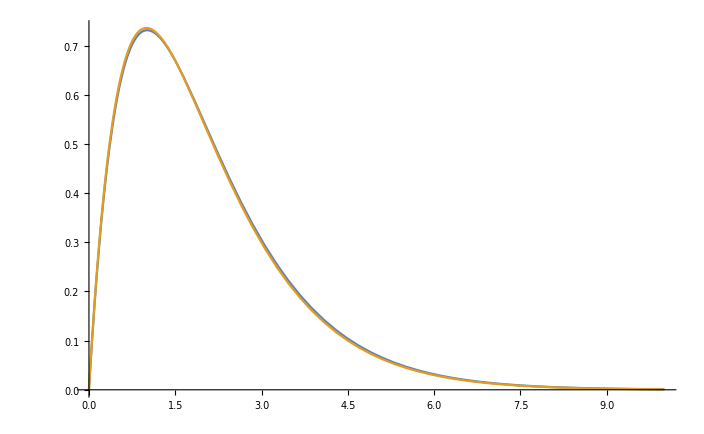

```mathematica
Plot[{Cs*u,d*2Exp[-d]},{d,0,10}]
```

```mathematica
L = Integrate[u^2,{d,0,Infinity}]
```

531441/128000

```mathematica
Cs = Sqrt[1/L]
```

(160 √5)/729

```mathematica
u
```

81 (9+4 (-9/4+d)) ⅇ^(-2-(11898637375327259732014097337769299293688798294769333508984283314041457376120344095867004824655472557675187999271853241203558591238905570206788084527321583066248582026784887234902132968060683571469513601058297562370160530340607849942554095557486780070414555603129323099649923489573350062357188314294245225987472417074007240612055747584770991072267007636764090438484359179546617239448259650885170465292981543834807042949776925329153470838724492488095529295189557924920125696980008 (-9/4+d))/11898637375327259732014097337769299293688798294769333508984283314041457376120344095867004824655472557675187999271853241203558591238905570206788084527321583066248582026784887234902132968060683571469513601058297562370160530340607849942554095557486780070414555603129323099649923489573350062357188314294245225987472417074007240612055747584770991072267007636764090438484359179546617239448259650885170465292981543834807042949776925329153470838724492488095529295189557924920125696980009)

```mathematica
Integrate[4d^2(Exp[-d])^2,{d,0,Infinity}]
```

1